### Problem 1: Matrices three ways

a) Create three 3x2 matrices (3 rows, 2 columns) and name them M1, M2, and M3 in the following ways: 
 (1) Create M1 by typing in entries directly as a list of lists.  
 
 (2) Use the Palette to create M2.  
 (3) Use Insert...Table/Matrix to create M3.  Use whatever values you like but make each matrix different.  Make use of these keyboard shortcuts:

b) Enter each matrix name to evaluate it and verify that it is a list of lists, regardless of the entry method

c) On another line use MatrixForm to view each matrix in standard format

```mathematica
(*a*)
	(*a1*)
	M1 = {{w,u},{v,x},{y,z}}
```

{{w,u},{v,x},{y,z}}

```mathematica
(*a2*)
	M2 = ({{6, 7}, {7, 8}, {8, 9}})
```

{{6,7},{7,8},{8,9}}

```mathematica
(*a3*)
	M3 = ({{-1, -2}, {2, 7}, {-4, -5}})
```

{{-1,-2},{2,7},{-4,-5}}

```mathematica
(*b*)
M1
```

{{w,u},{v,x},{y,z}}

```mathematica
M2
```

{{6,7},{7,8},{8,9}}

```mathematica
M3
```

{{-1,-2},{2,7},{-4,-5}}

```mathematica
(*c*)
M1 //MatrixForm
```

(w | u
v | x
y | z)

```mathematica
M2 //MatrixForm
```

(6 | 7
7 | 8
8 | 9)

```mathematica
M3//MatrixForm
```

(-1 | -2
2 | 7
-4 | -5)

### Problem 2: Matrix elements

```mathematica
M={{1,3},{2,2}};
M//MatrixForm
Eigensystem[M]
Eigensystem[M]//MatrixForm  (* easier to see what this matrix looks like if you put it in standard form *)
```

(1 | 3
2 | 2)

{{4,-1},{{1,1},{-3,2}}}

(4 | -1
{1,1} | {-3,2})

The two elements (4 and -1) in the first row are the two eigenvalues of M.  The two vectors {1,1} and {-3,2} in the second row are the eigenvectors associated with each of the eigenvalues.

a) Use the Part function (double brackets [[ ]]) to pull out the second eigenvalue (i.e. -1) from the matrix returned by Eigensystem[M]
b) Use double brackets to pull out the second eigenvector (i.e. {-3,2}) from the matrix returned by Eigensystem[M] 
c) Use double brackets to pull out the first element (i.e. -3) of the second eigenvector.  Hint: There are several ways to do this, including an extension of the “alternative” method described above.  See if you can do this with just ONE set of double-brackets

```mathematica
(*2a*)
Eigensystem[M][[1,2]]
```

-1

```mathematica
(*2b*)
Eigensystem[M][[2,2]]
```

{-3,2}

```mathematica
(*2c*)
Eigensystem[M][[2,2]][[1]]
```

-3

```mathematica
Eigensystem[M][[2,2,1]](*using only one set of double brackets*)
```

-3

### Problem 3: Determinants

(3.3.2 from HW#7) Find the determinant of:
	(5 | 17 | 3
2 | 4 | −3
11 | 0 | 2)

```mathematica
(*3*)
M3A = {{5,17,3},{2,4,-3},{11,0,2}}
```

{{5,17,3},{2,4,-3},{11,0,2}}

```mathematica
M3A//MatrixForm
```

(5 | 17 | 3
2 | 4 | -3
11 | 0 | 2)

```mathematica
Det[M3A]
```

-721

#### Problem 4: matrix inversion

(3.2.12 from HW 7)  a) Set up the following set of simultaneous equations in the form M.r = k, and solve for r (i.e. the vector whose components are the values of x, y, and z) using matrix inversion as in the example above. b) check your answer by multiplying the matrix M by the vector r and formatting using MatrixForm to see that it gives you k.
	2x + 5y + 1 = 2
	x + y + 2z = 1
	x + 5z = 3

```mathematica
(*4a*)
M4 = {{2,5,1},{1,1,2},{1,0,5}};
M4//MatrixForm
```

(2 | 5 | 1
1 | 1 | 2
1 | 0 | 5)

```mathematica
k4 = {{2},{1},{3}};
k4//MatrixForm
```

(2
1
3)

```mathematica
r4 = Inverse[M4].k4;
r4//MatrixForm
```

(-2
1
1)

```mathematica
(*b*)
M4.r4//MatrixForm
```

(2
1
3)

#### Problem 5: Eigenvectors & eigenvalues

(3.11.15 from HW 7)  a) Define the following matrix, then display it in standard form:  M=(2 | 3 | 0
3 | 2 | 0
0 | 0 | 1)
b) Find the eigenvalues and eigenvectors of M using the commands Eigenvalues and Eigenvectors.  Display the output of each, then see what it looks like in standard form using MatrixForm as well.
c) Use double brackets after the Eigenvectors command to pick out the second of the three eigenvectors.  Check to see that you did this correctly - the second eigenvector is the second row of the matrix output by the Eigenvectors command
d) Find the eigenvalues and eigenvectors of M using the command Eigensystem.  On another line, display the output in standard form.
e) Use double brackets to pick out the second eigenvalue from the Eigensystem command, and use double brackets to pick out its associated eigenvector.

```mathematica
(*5a*)
M5 = {{2,3,0},{3,2,0},{0,0,1}}
M5//MatrixForm
```

{{2,3,0},{3,2,0},{0,0,1}}

(2 | 3 | 0
3 | 2 | 0
0 | 0 | 1)

```mathematica
(*5b*)
M5b1=Eigenvalues[M5]
M5b2 = Eigenvectors[M5]
```

{5,-1,1}

{{1,1,0},{-1,1,0},{0,0,1}}

```mathematica
(*5b continued*)
M5b1 //MatrixForm
M5b2 //MatrixForm
```

(5
-1
1)

(1 | 1 | 0
-1 | 1 | 0
0 | 0 | 1)

```mathematica
(*5c*)
Eigenvectors[M5][[2]]
```

{-1,1,0}

```mathematica
(*5d*)
Eigensystem[M5]
```

{{5,-1,1},{{1,1,0},{-1,1,0},{0,0,1}}}

```mathematica
Eigensystem[M5]//MatrixForm
```

(5 | -1 | 1
{1,1,0} | {-1,1,0} | {0,0,1})

```mathematica
(*5e*)
Eigensystem[M5][[1,2]]
```

-1

```mathematica
Eigensystem[M5][[2,2]]
```

{-1,1,0}

### Problem 6. Coupled harmonic oscillators, normal modes

For simplicity, let's set m = 1 and k_s=k_b=1 for some choice of units. 
a) Create the matrix M of spring constants and the vector r containing the initial positions u_0 and v_0.
b) Use Mathematica to solve the eigenvalue equation and determine what two frequencies are allowed, along with what the relationship is between u_0 and v_0 for each allowed frequency. 
c) Compare the two frequencies of the two modes to the frequency the masses would have if they were not coupled together. Qualitatively explain why the allowed frequencies are higher, lower, or the same as the uncoupled case.

```mathematica
(*6a*)
M = {{2,-1},{-1,2}};
M //MatrixForm
```

(2 | -1
-1 | 2)

```mathematica
r = {{Subscript[u, 0]},{Subscript[v, 0]}};
r //MatrixForm
```

(u_0
v_0)

```mathematica
(*6b*)
Eigensystem[M]//MatrixForm
```

(3 | 1
{-1,1} | {1,1})

```mathematica
Ω = Sqrt[Eigensystem[M]];
Ω//MatrixForm
```

(√3 | 1
{ⅈ,1} | {1,1})

```mathematica
ω1 = Ω[[1,1]]
ω2 = Ω[[1,2]]
```

√3

1

```mathematica
(*6c*)
(*uncoupled frequencies*)
ωO1 = Sqrt[1/1]
ωO2 = Sqrt[1/1]
```

1

1

Each mass would have an uncoupled frequency of 1. Qualitatively this makes sense that the coupled frequencies would be greater than or equal to their uncoupled frequencies. This is because with more springs in the system, there could only be an increase in oscillation since more spring force is applied.

```mathematica
(*please run these before the next problem. They will not output anything but the info needs to be made*)
omega1=Sqrt[Eigensystem[M][[1,1]]/m]/.m->1;
omega2=Sqrt[Eigensystem[M][[1,2]]/m]/.m->1;
uinit1=Eigensystem[M][[2,1,1]];
vinit1=Eigensystem[M][[2,1,2]];
uinit2=Eigensystem[M][[2,2,1]];
vinit2=Eigensystem[M][[2,2,2]];
upos1[t_]=uinit1*Cos[omega1*t];
vpos1[t_]=vinit1*Cos[omega1*t];
upos2[t_]=uinit2*Cos[omega2*t];
vpos2[t_]=vinit2*Cos[omega2*t];
```

### Problem 7. Coupled harmonic oscillators, plots

a) Plot the positions of the masses as a function of time for the first normal mode.  Plot them both on the same graph.
b) Repeat for normal mode 2

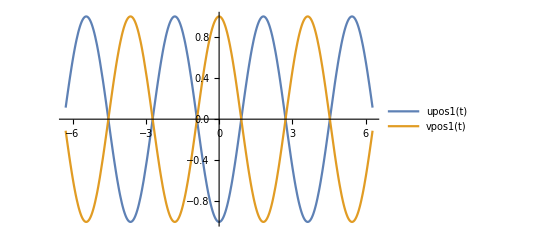

```mathematica
(*7a*)
Plot[{upos1[t],vpos1[t]},{t,-2*Pi,2*Pi},PlotLegends->"Expressions"]
```

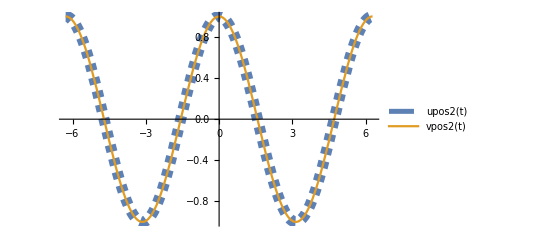

```mathematica
(*7b*)
Plot[{upos2[t],vpos2[t]},{t,-2*Pi,2*Pi},PlotStyle->{{Thickness[0.02],Dashed},{Thick}}, PlotLegends->"Expressions"]
```

### Problem 8. Coupled harmonic oscillators, general solution

If you shook this oscillator to get it moving it probably would NOT oscillate in a normal mode.  So what good are they?  The normal modes of oscillation are important because they serve as “basis functions” from which you can build ANY general oscillation.  As a simple example, let’s construct an oscillation by adding together equal amounts of the two normal modes - so the oscillation will be 1/2 mode 1 + 1/2 mode 2.  Then for example the position of mass 1 will be 1/2 upos1[t]+1/2 upos2[t].  
a) Make a plot of the two masses undergoing this type of vibration
b) Does the oscillation pattern repeat itself?  Do the two masses have the same oscillation frequencies?

```mathematica
(*8a*)
unew1[t_]=(1/2)upos1[t]+(1/2)upos2[t]
vnew1[t_]=(1/2)vpos1[t]+(1/2)vpos2[t]
```

Cos[t]/2-1/2 Cos[√3 t]

Cos[t]/2+1/2 Cos[√3 t]

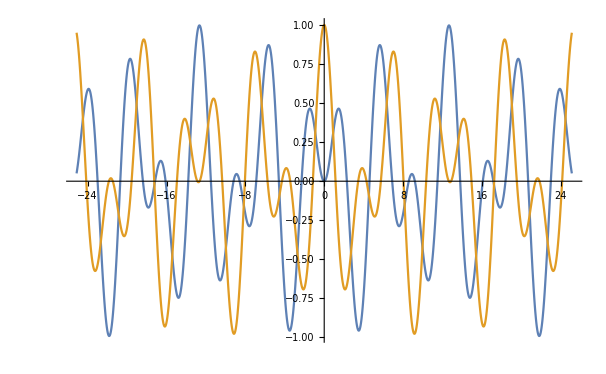

```mathematica
Plot[{unew1[t],vnew1[t]},{t,-8*Pi,8*Pi}]
```

(*8b*)
Yes, the oscillation pattern does repeat itself. 

The masses do have the same oscillation frequencies. This is clear since the two waves have the same period, thus the reciprocal of this period (the frequency) must also be the same.

```mathematica
x0=1.5 (* equilib positions of the masses are at ±x0 *);
xwall=3.5 (* wall positions are at ±xwall *);
wallgraphics={Thick,Black,Line[{{-xwall,-.5},{-xwall,.5}}],Line[{{xwall,-.5},{xwall,.5}}],Thin,Line[{{-x0,-.1},{-x0,.1}}],Line[{{x0,-.1},{x0,.1}}]};
```

### Problem 9. Coupled harmonic oscillators, animation

a) Modify the animation above to include the second oscillating mass and the other two springs.  Give them all different colors.  Mathematica recognizes color names such as Blue, Yellow, Red, Green, Magenta, Brown, Black, White, and others.  Mathematica draws the object in the order you list them, so you may have to play around with the order in which you call them to get them placed properly in front of or behind other objects.

b) When you have finished (a), copy & paste the animation command to another line, then modify it so that it shows the second normal mode.

```mathematica
(*upos1 & vpos1*)
Animate[Graphics[{Thick,Magenta,Line[{{-x0+upos1[t],0},{x0+vpos1[t],0}}],Blue,Ball[{-x0+upos1[t],0},.15],Line[{{-xwall,0},{-x0+upos1[t],0}}],Green,Line[{{xwall,0},{x0+vpos1[t],0}}],Ball[{x0+vpos1[t],0},.15]},PlotRange->{{-xwall,xwall},{-1,1}}],{t,0,50},AnimationRate->2]
```

```mathematica
(*upos2 & vpos2*)
Animate[Graphics[{Thick,Magenta,Line[{{-x0+upos2[t],0},{x0+vpos2[t],0}}],Blue,Ball[{-x0+upos2[t],0},.15],Line[{{-xwall,0},{-x0+upos2[t],0}}],Green,Line[{{xwall,0},{x0+vpos2[t],0}}],Ball[{x0+vpos2[t],0},.15]},PlotRange->{{-xwall,xwall},{-1,1}}],{t,0,50},AnimationRate->2]
```

```mathematica
(*unew1 & vnew1*)
(*this one was just out of curiousity*)
Animate[Graphics[{Thick,Magenta,Line[{{-x0+unew1[t],0},{x0+vnew1[t],0}}],Blue,Ball[{-x0+unew1[t],0},.15],Line[{{-xwall,0},{-x0+unew1[t],0}}],Green,Line[{{xwall,0},{x0+vnew1[t],0}}],Ball[{x0+vnew1[t],0},.15]},PlotRange->{{-xwall,xwall},{-1,1}}],{t,0,50},AnimationRate->2]
```

What to turn in
When you are done, SAVE this entire file, with all your work.  Then SAVE it again under the new name “HW#10-yourname”, where yourname is of course, your name.  Delete all but the Assignments themselves (of which there are 9).  Make sure the entire worksheet runs correctly and that you haven’t deleted anything important!  Turn in this assignment worksheet, with all of its input and output code, through the link on our Moodle page.